Il file é una copia di muvbf.nb, a parte la sintassi per l’esportazione dei plot.

correzione dovuta a alpha hardcoded in PhotonFlux

```mathematica
alpharescale=137/132.507
```

1.03391

Le solite funzioni per maneggiare istogrammi

```mathematica
rapp[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]/x2[[i,2]]},{i,1,Length[x1]}]
absrapp[x1_,x2_]:=Table[{x1[[i,1]],Abs[x1[[i,2]]/x2[[i,2]]]},{i,1,Length[x1]}]
mult[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]*x2[[i,2]]},{i,1,Length[x1]}]
sum[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]+x2[[i,2]]},{i,1,Length[x1]}]
sumlist[x1_]:=Table[{x1[[1,i,1]],x1[[1,i,2]]+x1[[2,i,2]]+x1[[3,i,2]]},{i,1,Length[x1[[1]]]}]
coeff[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]*c},{i,1,Length[x1]}]
sumconst[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]+c},{i,1,Length[x1]}]
diff[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]-x2[[i,2]]},{i,1,Length[x1]}]
joinbin[x_,n_]:=Map[{(Plus@@#)[[1]]/n,(Plus@@#)[[2]]}&,Partition[x,n]]
```

Nome del Run

```mathematica
(*nome="again";*)
nome="PDF1sttryMSbar";
```

Seleziona i vari input guarda il README per capire chi é chi

```mathematica
aaWWdata=Import["/Users/pagani/mg5_3.5/aatottformuu/"<>nome<>".dat"];

aadata=Import["/Users/pagani/mg5_3.5/mupemtomupemtt_v0/"<>nome<>".dat"];
muadata=Import["/Users/pagani/mg5_3.5/mupemtomupemtt/"<>nome<>".dat"];
muaWWdata=Import["/Users/pagani/mg5_3.5/altottl/"<>nome<>".dat"];
nocutsmuaWWdata=Import["/Users/pagani/mg5_3.5/nocuts_altottl/"<>nome<>".dat"];
mumudata=Import["/Users/pagani/mg5_3.5/mupemtomupemtt_v2/"<>nome<>".dat"];

OPaadata=Import["/Users/pagani/mg5_3.5/onlyphoton_mupemtomupemtt_v0/"<>nome<>".dat"];
OPmuadata=Import["/Users/pagani/mg5_3.5/onlyphoton_mupemtomupemtt/"<>nome<>".dat"];
OPmuaWWdata=Import["/Users/pagani/mg5_3.5/onlyphoton_altottl/"<>nome<>".dat"];
OPnocutsmuaWWdata=Import["/Users/pagani/mg5_3.5/onlyphoton_nocuts_altottl/"<>nome<>".dat"];
OPmumudata=Import["/Users/pagani/mg5_3.5/onlyphoton_mupemtomupemtt_v2/"<>nome<>".dat"];
```

Qui devo impostare a mano come é lo scan in pt=mufac,  Table[{   fattorediscaling^i,   XXdata  [[i+5,3]]},  {i,i minima,i massima}]


Dopo poi definisco a mano il valore di total, cioé no cut, e lo stesso senza fotoni (NP) o con solo fotoni (OP).
In generale OP vuol dire “senza fotoni”. Chiaramente con solo Z vuol dire total-(NPtotal+OPtotal)
Riscalo anche con l’alpha giusta ...

```mathematica
aaWW=Table[{1.5^i,aaWWdata[[i+5,3]]},{i,-4,19}];
aa=Table[{1.5^i,aadata[[i+5,3]]},{i,-4,19}];

aa=Table[{1.5^i,aadata[[i+5,3]]},{i,-4,19}];
mua=Table[{1.5^i,muadata[[i+5,3]]},{i,-4,19}];
muaWW=Table[{1.5^i,muaWWdata[[i+5,3]]},{i,-4,19}];
nocutsmuaWW=Table[{1.5^i,nocutsmuaWWdata[[i+5,3]]},{i,-4,19}];
mumu=Table[{1.5^i,mumudata[[i+5,3]]},{i,-4,19}];

OPaa=Table[{1.5^i,OPaadata[[i+5,3]]},{i,-4,19}];
OPmua=Table[{1.5^i,OPmuadata[[i+5,3]]},{i,-4,19}];
OPmuaWW=Table[{1.5^i,OPmuaWWdata[[i+5,3]]},{i,-4,19}];
OPnocutsmuaWW=Table[{1.5^i,OPnocutsmuaWWdata[[i+5,3]]},{i,-4,19}];
OPmumu=Table[{1.5^i,OPmumudata[[i+5,3]]},{i,-4,19}];


aaWW=coeff[aaWW,alpharescale^2];
muaWW=coeff[muaWW,alpharescale];
nocutsmuaWW=coeff[nocutsmuaWW,alpharescale];
OPmuaWW=coeff[OPmuaWW,alpharescale];
OPnocutsmuaWW=coeff[OPnocutsmuaWW,alpharescale];



total=Table[{1.5^i,0.02984},{i,-4,19}];
NPtotal=Table[{1.5^i,0.000428},{i,-4,19}];
OPtotal=Table[{1.5^i,0.01946},{i,-4,19}];
ZPtotal=diff[total,sum[NPtotal,OPtotal]];

summed=sum[mumu,sum[aa,mua]];
summedWWa=sum[mumu,sum[aaWW,muaWW]];
OPsummed=sum[OPmumu,sum[OPaa,OPmua]];
OPsummedWWa=sum[OPmumu,sum[aaWW,OPmuaWW]];

aaplusmumu=sum[aa,mumu];
aaplusmua=sum[aa,mua];
```

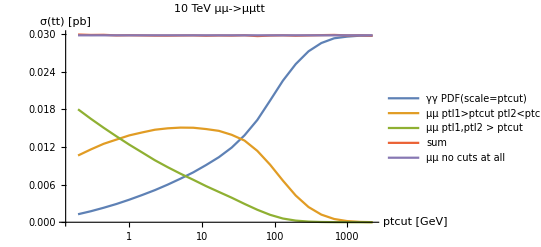

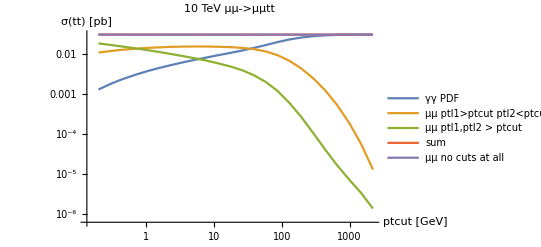

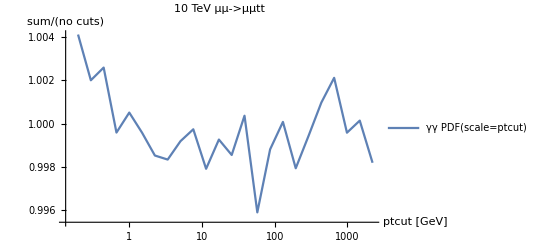

```mathematica
linearplot=ListLogLinearPlot[{aa,mua,mumu,summed,total},Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt",AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{"γγ PDF(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μμ ptl1,ptl2 > ptcut", "sum","μμ no cuts at all"}]
logplot=ListLogLogPlot[{aa,mua,mumu,summed,total},Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt",AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{"γγ PDF", "μμ ptl1>ptcut ptl2<ptcut", "μμ ptl1,ptl2 > ptcut", "sum","μμ no cuts at all"}]

ratioplot=ListLogLinearPlot[rapp[summed,total],Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt",AxesLabel->{"ptcut [GeV]","sum/(no cuts)"},LabelStyle->{FontSize->15},PlotLegends->{"γγ PDF(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μμ ptl1,ptl2 > ptcut", "sum","μμ no cuts at all"}]
```

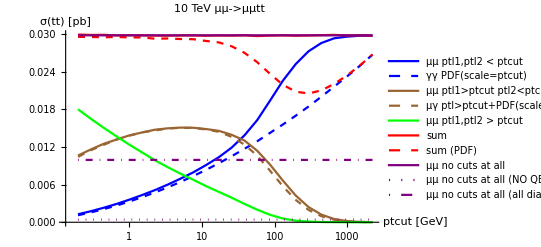

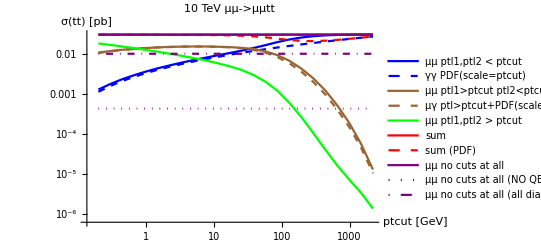

```mathematica
linearplotWWa=ListLogLinearPlot[{aa,aaWW,mua, muaWW,mumu,summed,summedWWa,total,NPtotal,ZPtotal},Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt",AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ PDF(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+PDF(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (PDF)","μμ no cuts at all","μμ no cuts at all (NO QED)","μμ no cuts at all (all diag -(only QED + NO QED))"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple,{Purple,Dotted},{Purple,DotDashed}}]
logplotWWa=ListLogLogPlot[{aa,aaWW,mua, muaWW,mumu,summed,summedWWa,total,NPtotal,ZPtotal},Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt",AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ PDF(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+PDF(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (PDF)","μμ no cuts at all","μμ no cuts at all (NO QED)","μμ no cuts at all (all diag -(only QED + NO QED))"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple,{Purple,Dotted},{Purple,DotDashed}}]
```

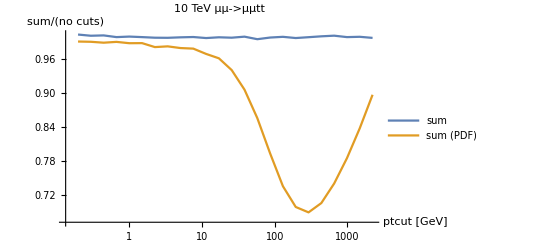

```mathematica
ratioplotWWa=ListLogLinearPlot[{rapp[summed,total],rapp[summedWWa,total]},Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt",AxesLabel->{"ptcut [GeV]","sum/(no cuts)"},LabelStyle->{FontSize->15},PlotLegends->{"sum","sum (PDF)"}]
```

```mathematica
RHS2nd82=diff[mua, muaWW];
RHS3rd=diff[aa, aaWW];
```

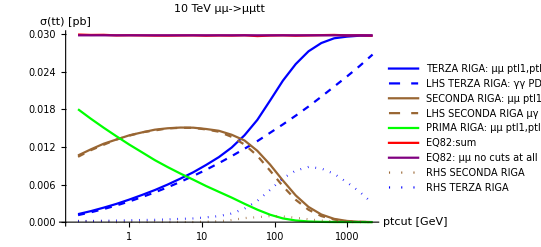

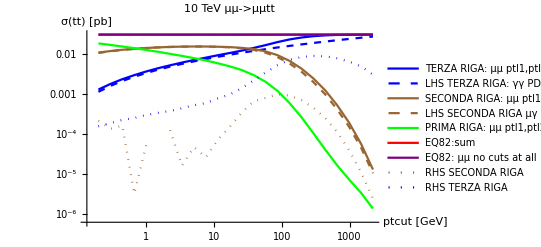

```mathematica
linearplotEQ82=ListLogLinearPlot[{aa,aaWW,mua, muaWW,mumu,summed,total,RHS2nd82, RHS3rd},Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt",AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{"TERZA RIGA: μμ ptl1,ptl2 < ptcut","LHS TERZA RIGA: γγ PDF(scale=ptcut)", "SECONDA RIGA: μμ ptl1>ptcut ptl2<ptcut", "LHS SECONDA RIGA μγ ptl>ptcut+PDF(scale=ptcut)", "PRIMA RIGA: μμ ptl1,ptl2 > ptcut", "EQ82:sum"(*,"sum (PDF)"*),"EQ82: μμ no cuts at all","RHS SECONDA RIGA","RHS TERZA RIGA"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,Purple,{Brown,Dotted},{Blue,Dotted}}]
logplotEQ82=ListLogLogPlot[{aa,aaWW,mua, muaWW,mumu,summed,total,RHS2nd82, RHS3rd},Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt",AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{"TERZA RIGA: μμ ptl1,ptl2 < ptcut","LHS TERZA RIGA: γγ PDF(scale=ptcut)", "SECONDA RIGA: μμ ptl1>ptcut ptl2<ptcut", "LHS SECONDA RIGA μγ ptl>ptcut+PDF(scale=ptcut)", "PRIMA RIGA: μμ ptl1,ptl2 > ptcut", "EQ82:sum"(*,"sum (PDF)"*),"EQ82: μμ no cuts at all","RHS SECONDA RIGA","RHS TERZA RIGA"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,Purple,{Brown,Dotted},{Blue,Dotted}}]
```

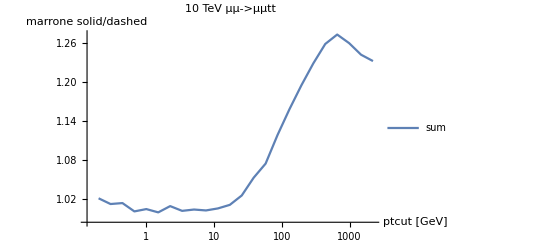

```mathematica
ratioplotmuaWW=ListLogLinearPlot[{rapp[mua,muaWW]},Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt",AxesLabel->{"ptcut [GeV]","marrone solid/dashed"},LabelStyle->{FontSize->15},PlotLegends->{"sum","sum (PDF)"}]
```

```mathematica
Export["/Users/pagani/mu-vbf/massive_mu/plots_PDF/"<>nome<>"/linearplot.pdf",linearplotWWa]
Export["/Users/pagani/mu-vbf/massive_mu/plots_PDF/"<>nome<>"/logplot.pdf",logplotWWa]
Export["/Users/pagani/mu-vbf/massive_mu/plots_PDF/"<>nome<>"/ratioplot.pdf",ratioplotWWa]
Export["/Users/pagani/mu-vbf/massive_mu/plots_PDF/"<>nome<>"/ratioplotmua.pdf",ratioplotmuaWW]


Export["/Users/pagani/mu-vbf/massive_mu/plots_PDF/"<>nome<>"/EQ82/linearplot.pdf",linearplotEQ82]
Export["/Users/pagani/mu-vbf/massive_mu/plots_PDF/"<>nome<>"//EQ82/logplot.pdf",logplotEQ82]
```

/Users/pagani/mu-vbf/massive_mu/plots_PDF/PDF1sttryMSbar/linearplot.pdf

/Users/pagani/mu-vbf/massive_mu/plots_PDF/PDF1sttryMSbar/logplot.pdf

/Users/pagani/mu-vbf/massive_mu/plots_PDF/PDF1sttryMSbar/ratioplot.pdf

/Users/pagani/mu-vbf/massive_mu/plots_PDF/PDF1sttryMSbar/ratioplotmua.pdf

/Users/pagani/mu-vbf/massive_mu/plots_PDF/PDF1sttryMSbar/EQ82/linearplot.pdf

/Users/pagani/mu-vbf/massive_mu/plots_PDF/PDF1sttryMSbar//EQ82/logplot.pdf

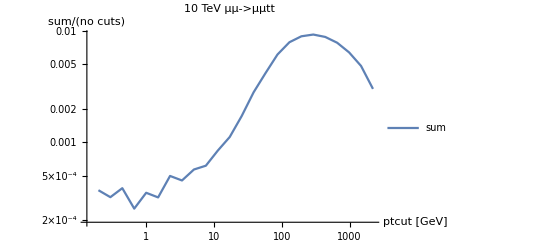

```mathematica
ListLogLogPlot[diff[summed,summedWWa],Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt",AxesLabel->{"ptcut [GeV]","sum/(no cuts)"},LabelStyle->{FontSize->15},PlotLegends->{"sum","sum (PDF)"}]
```

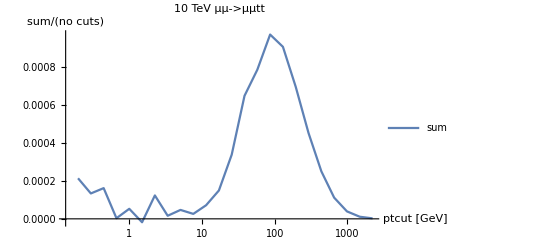

```mathematica
ListLogLinearPlot[diff[mua,muaWW],Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt",AxesLabel->{"ptcut [GeV]","sum/(no cuts)"},LabelStyle->{FontSize->15},PlotLegends->{"sum","sum (PDF)"}]
```

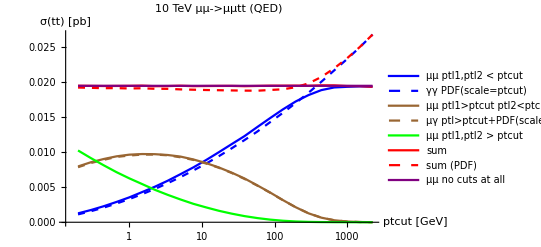

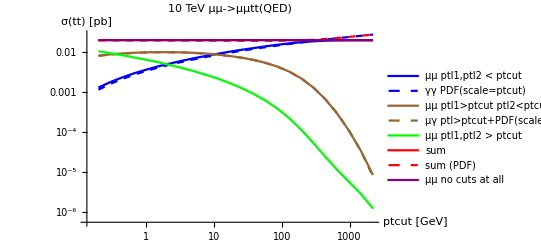

```mathematica
OPlinearplotWWa=ListLogLinearPlot[{OPaa,aaWW,OPmua, OPmuaWW,OPmumu,OPsummed,OPsummedWWa,OPtotal},Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt (QED)",AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ PDF(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+PDF(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (PDF)","μμ no cuts at all"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple}]
OPlogplotWWa=ListLogLogPlot[{OPaa,aaWW,OPmua, OPmuaWW,OPmumu,OPsummed,OPsummedWWa,OPtotal},Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt(QED)",AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ PDF(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+PDF(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (PDF)","μμ no cuts at all"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple}]
```

```mathematica
OPRHS2nd82=diff[OPmua, OPmuaWW];
OPRHS3rd=diff[OPaa, aaWW];
```

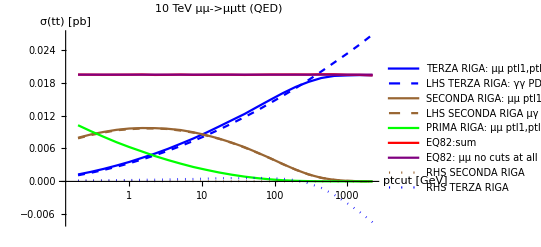

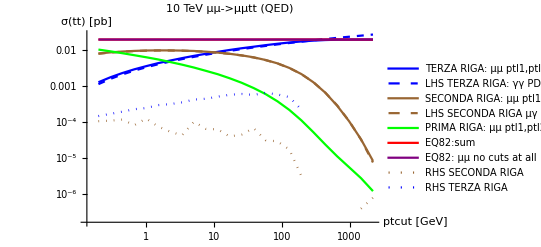

```mathematica
OPlinearplotEQ82=ListLogLinearPlot[{OPaa,aaWW,OPmua, OPmuaWW,OPmumu,OPsummed,OPtotal,OPRHS2nd82, OPRHS3rd},Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt (QED)",AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{"TERZA RIGA: μμ ptl1,ptl2 < ptcut","LHS TERZA RIGA: γγ PDF(scale=ptcut)", "SECONDA RIGA: μμ ptl1>ptcut ptl2<ptcut", "LHS SECONDA RIGA μγ ptl>ptcut+PDF(scale=ptcut)", "PRIMA RIGA: μμ ptl1,ptl2 > ptcut", "EQ82:sum"(*,"sum (PDF)"*),"EQ82: μμ no cuts at all","RHS SECONDA RIGA","RHS TERZA RIGA"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,Purple,{Brown,Dotted},{Blue,Dotted}}]
OPlogplotEQ82=ListLogLogPlot[{OPaa,aaWW,OPmua, OPmuaWW,OPmumu,OPsummed,OPtotal,OPRHS2nd82, OPRHS3rd},Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt (QED)",AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{"TERZA RIGA: μμ ptl1,ptl2 < ptcut","LHS TERZA RIGA: γγ PDF(scale=ptcut)", "SECONDA RIGA: μμ ptl1>ptcut ptl2<ptcut", "LHS SECONDA RIGA μγ ptl>ptcut+PDF(scale=ptcut)", "PRIMA RIGA: μμ ptl1,ptl2 > ptcut", "EQ82:sum"(*,"sum (PDF)"*),"EQ82: μμ no cuts at all","RHS SECONDA RIGA","RHS TERZA RIGA"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,Purple,{Brown,Dotted},{Blue,Dotted}}]
```

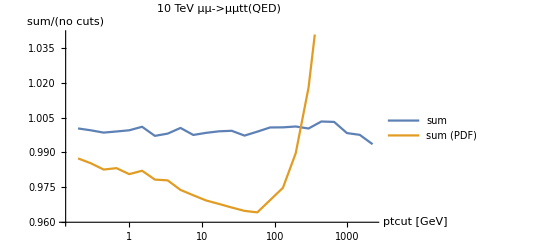

```mathematica
OPratioplotWWa=ListLogLinearPlot[{rapp[OPsummed,OPtotal],rapp[OPsummedWWa,OPtotal]},Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt(QED)",AxesLabel->{"ptcut [GeV]","sum/(no cuts)"},LabelStyle->{FontSize->15},PlotLegends->{"sum","sum (PDF)"}]
```

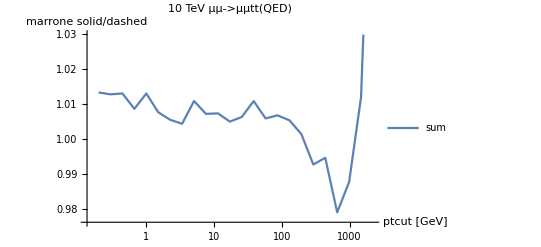

```mathematica
OPratioplotmuaWW=ListLogLinearPlot[{rapp[OPmua,OPmuaWW]},Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt(QED)",AxesLabel->{"ptcut [GeV]","marrone solid/dashed"},LabelStyle->{FontSize->15},PlotLegends->{"sum","sum (PDF)"}]
```

```mathematica
Export["/Users/pagani/mu-vbf/massive_mu/plots_PDF/"<>nome<>"/OPlinearplot.pdf",OPlinearplotWWa]
Export["/Users/pagani/mu-vbf/massive_mu/plots_PDF/"<>nome<>"/OPlogplot.pdf",OPlogplotWWa]
Export["/Users/pagani/mu-vbf/massive_mu/plots_PDF/"<>nome<>"/OPratioplot.pdf",OPratioplotWWa]
Export["/Users/pagani/mu-vbf/massive_mu/plots_PDF/"<>nome<>"/OPratioplotmua.pdf",OPratioplotmuaWW]



Export["/Users/pagani/mu-vbf/massive_mu/plots_PDF/"<>nome<>"/EQ82/OPlinearplot.pdf",OPlinearplotEQ82]
Export["/Users/pagani/mu-vbf/massive_mu/plots_PDF/"<>nome<>"//EQ82/OPlogplot.pdf",OPlogplotEQ82]
```

/Users/pagani/mu-vbf/massive_mu/plots_PDF/PDF1sttryMSbar/OPlinearplot.pdf

/Users/pagani/mu-vbf/massive_mu/plots_PDF/PDF1sttryMSbar/OPlogplot.pdf

/Users/pagani/mu-vbf/massive_mu/plots_PDF/PDF1sttryMSbar/OPratioplot.pdf

/Users/pagani/mu-vbf/massive_mu/plots_PDF/PDF1sttryMSbar/OPratioplotmua.pdf

/Users/pagani/mu-vbf/massive_mu/plots_PDF/PDF1sttryMSbar/EQ82/OPlinearplot.pdf

/Users/pagani/mu-vbf/massive_mu/plots_PDF/PDF1sttryMSbar//EQ82/OPlogplot.pdf

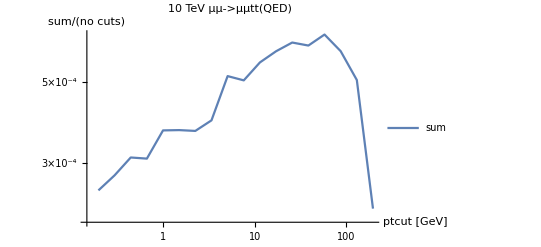

```mathematica
ListLogLogPlot[diff[OPsummed,OPsummedWWa],Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt(QED)",AxesLabel->{"ptcut [GeV]","sum/(no cuts)"},LabelStyle->{FontSize->15},PlotLegends->{"sum","sum (PDF)"}]
```

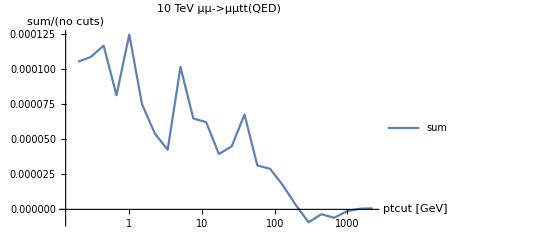

```mathematica
ListLogLinearPlot[diff[OPmua,OPmuaWW],Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt(QED)",AxesLabel->{"ptcut [GeV]","sum/(no cuts)"},LabelStyle->{FontSize->15},PlotLegends->{"sum","sum (PDF)"}]
```

```mathematica
muaWWminus2aa=diff[nocutsmuaWW,coeff[aaWW,2]];
nodiv=diff[total,sum[aaWW,muaWWminus2aa]];
OPmuaWWminus2aa=diff[OPnocutsmuaWW,coeff[aaWW,2]];
OPnodiv=diff[OPtotal,sum[aaWW,OPmuaWWminus2aa]];
```

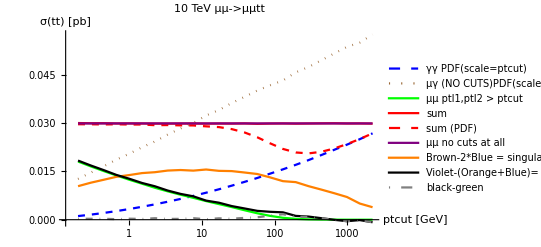

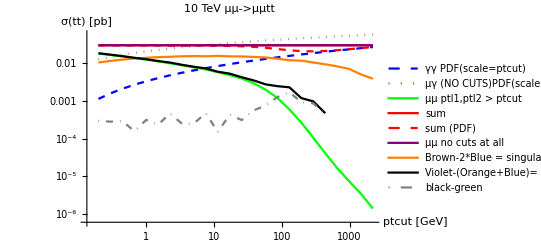

```mathematica
linearplotdiv=ListLogLinearPlot[{aaWW,nocutsmuaWW,mumu,summed,summedWWa,total,muaWWminus2aa,nodiv,diff[nodiv,mumu]},Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt ",AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{ "γγ PDF(scale=ptcut)","μγ (NO CUTS)PDF(scale=ptcut)","μμ ptl1,ptl2 > ptcut", "sum","sum (PDF)","μμ no cuts at all","Brown-2*Blue = singular div.", "Violet-(Orange+Blue)= μμ no cuts at all - (singular + double div.) ", "black-green"},PlotStyle->{{Blue,Dashed},{Brown,Dotted},Green,Red,{Red,Dashed},Purple,Orange,Black,{Gray,DotDashed}}]
logplotdiv=ListLogLogPlot[{aaWW,nocutsmuaWW,mumu,summed,summedWWa,total,muaWWminus2aa,nodiv,diff[nodiv,mumu]},Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt ",AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{ "γγ PDF(scale=ptcut)","μγ (NO CUTS)PDF(scale=ptcut)","μμ ptl1,ptl2 > ptcut", "sum","sum (PDF)","μμ no cuts at all","Brown-2*Blue = singular div.", "Violet-(Orange+Blue)= μμ no cuts at all - (singular + double div.) ", "black-green"},PlotStyle->{{Blue,Dashed},{Brown,Dotted},Green,Red,{Red,Dashed},Purple,Orange,Black,{Gray,DotDashed}}]
```

```mathematica
(*nel bu ho invece RHS2nd83=diff[mua, nocutsmuaWW]*)
ddelta2S= diff[nocutsmuaWW,coeff[aaWW,2]];
RHS2nd83=diff[mua, ddelta2S];
```

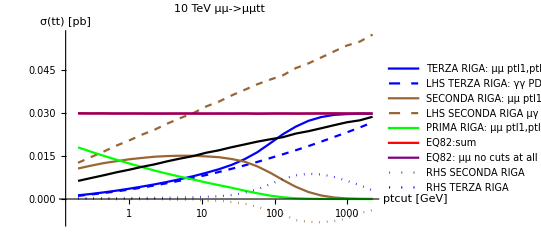

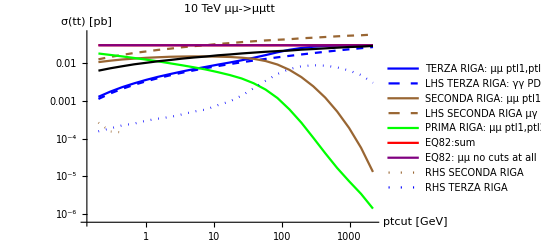

```mathematica
linearplotEQ83=ListLogLinearPlot[{aa,aaWW,mua, nocutsmuaWW,mumu,summed,total, RHS2nd83,RHS3rd,coeff[ nocutsmuaWW,0.5]},Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt",AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{"TERZA RIGA: μμ ptl1,ptl2 < ptcut","LHS TERZA RIGA: γγ PDF(scale=ptcut)", "SECONDA RIGA: μμ ptl1>ptcut ptl2<ptcut", "LHS SECONDA RIGA μγ (NOCUT) PDF(scale=ptcut)", "PRIMA RIGA: μμ ptl1,ptl2 > ptcut", "EQ82:sum"(*,"sum (WeizWill)"*),"EQ82: μμ no cuts at all","RHS SECONDA RIGA","RHS TERZA RIGA"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,Purple,{Brown,Dotted},{Blue,Dotted},Black}]
logplotEQ83=ListLogLogPlot[{aa,aaWW,mua, nocutsmuaWW,mumu,summed,total, RHS2nd83,RHS3rd,coeff[ nocutsmuaWW,0.5]},Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt",AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{"TERZA RIGA: μμ ptl1,ptl2 < ptcut","LHS TERZA RIGA: γγ PDF(scale=ptcut)", "SECONDA RIGA: μμ ptl1>ptcut ptl2<ptcut", "LHS SECONDA RIGA μγ (NOCUT) PDF(scale=ptcut)", "PRIMA RIGA: μμ ptl1,ptl2 > ptcut", "EQ82:sum"(*,"sum (WeizWill)"*),"EQ82: μμ no cuts at all","RHS SECONDA RIGA","RHS TERZA RIGA"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,Purple,{Brown,Dotted},{Blue,Dotted},Black}]
```

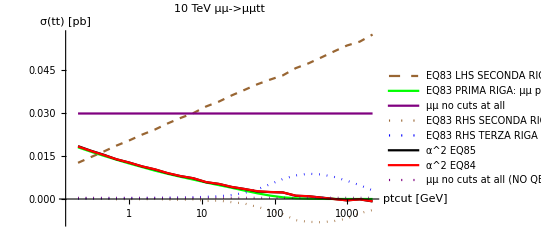

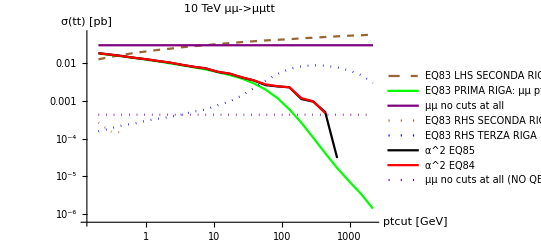

```mathematica
linearplotEQ85=ListLogLinearPlot[{(*aa,aaWW,mua,*) nocutsmuaWW,mumu,(*summed,*)total, RHS2nd83,RHS3rd(*,coeff[nocutsmuaWW,0.5]*),sum[sum[mumu,RHS2nd83],RHS3rd],diff[total,sum[ddelta2S,aaWW]],NPtotal},Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt ",AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{(*"TERZA RIGA: μμ ptl1,ptl2 < ptcut","LHS TERZA RIGA: γγ PDF(scale=ptcut)", "SECONDA RIGA: μμ ptl1>ptcut ptl2<ptcut",*) "EQ83 LHS SECONDA RIGA μγ (NOCUT) PDF(scale=ptcut)", "EQ83 PRIMA RIGA: μμ ptl1,ptl2 > ptcut"(*, "EQ83:sum","sum (PDF)"*),"μμ no cuts at all","EQ83 RHS SECONDA RIGA","EQ83 RHS TERZA RIGA",(*"(LHS SECONDA RIGA)/2",*)"α^2 EQ85","α^2 EQ84","μμ no cuts at all (NO QED)"},PlotStyle->{(*Blue,{Blue,Dashed},Brown,*){Brown,Dashed},Green,(*Red,*)Purple,{Brown,Dotted},{Blue,Dotted},(*Black,*){Black,Thickness->0.01},{Red,Thickness->0.01},{Purple,Dotted}}]

logplotEQ85=ListLogLogPlot[{(*aa,aaWW,mua,*) nocutsmuaWW,mumu,(*summed,*)total, RHS2nd83,RHS3rd(*,coeff[nocutsmuaWW,0.5]*),sum[sum[mumu,RHS2nd83],RHS3rd],diff[total,sum[ddelta2S,aaWW]],NPtotal},Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt ",AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{(*"TERZA RIGA: μμ ptl1,ptl2 < ptcut","LHS TERZA RIGA: γγ PDF(scale=ptcut)", "SECONDA RIGA: μμ ptl1>ptcut ptl2<ptcut",*) "EQ83 LHS SECONDA RIGA μγ (NOCUT) PDF(scale=ptcut)", "EQ83 PRIMA RIGA: μμ ptl1,ptl2 > ptcut"(*, "EQ83:sum","sum (PDF)"*),"μμ no cuts at all","EQ83 RHS SECONDA RIGA","EQ83 RHS TERZA RIGA",(*"(LHS SECONDA RIGA)/2",*)"α^2 EQ85","α^2 EQ84","μμ no cuts at all (NO QED)"},PlotStyle->{(*Blue,{Blue,Dashed},Brown,*){Brown,Dashed},Green,(*Red,*)Purple,{Brown,Dotted},{Blue,Dotted},(*Black,*){Black,Thickness->0.01},{Red,Thickness->0.01},{Purple,Dotted}}]
```

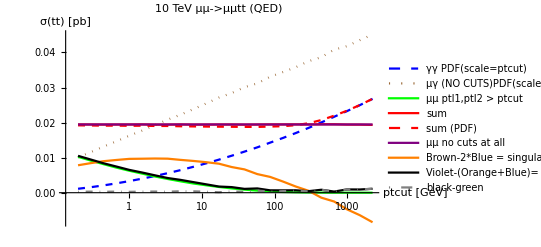

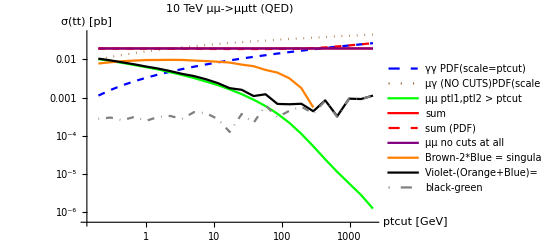

```mathematica
OPlinearplotdiv=ListLogLinearPlot[{aaWW,OPnocutsmuaWW,OPmumu,OPsummed,OPsummedWWa,OPtotal,OPmuaWWminus2aa,OPnodiv,diff[OPnodiv,OPmumu]},Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt (QED)",AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{ "γγ PDF(scale=ptcut)","μγ (NO CUTS)PDF(scale=ptcut)","μμ ptl1,ptl2 > ptcut", "sum","sum (PDF)","μμ no cuts at all","Brown-2*Blue = singular div.", "Violet-(Orange+Blue)= μμ no cuts at all - (singular + double div.) ", "black-green"},PlotStyle->{{Blue,Dashed},{Brown,Dotted},Green,Red,{Red,Dashed},Purple,Orange,Black,{Gray,DotDashed}}]
OPlogplotdiv=ListLogLogPlot[{aaWW,OPnocutsmuaWW,OPmumu,OPsummed,OPsummedWWa,OPtotal,OPmuaWWminus2aa,OPnodiv,diff[OPnodiv,OPmumu]},Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt (QED)",AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{ "γγ PDF(scale=ptcut)","μγ (NO CUTS)PDF(scale=ptcut)","μμ ptl1,ptl2 > ptcut", "sum","sum (PDF)","μμ no cuts at all","Brown-2*Blue = singular div.", "Violet-(Orange+Blue)= μμ no cuts at all - (singular + double div.) ", "black-green"},PlotStyle->{{Blue,Dashed},{Brown,Dotted},Green,Red,{Red,Dashed},Purple,Orange,Black,{Gray,DotDashed}}]
```

```mathematica
Export["/Users/pagani/mu-vbf/massive_mu/plots_PDF/"<>nome<>"/OPlinearplotdiv.pdf",OPlinearplotdiv]
Export["/Users/pagani/mu-vbf/massive_mu/plots_PDF/"<>nome<>"/OPlogplotdiv.pdf",OPlogplotdiv]
Export["/Users/pagani/mu-vbf/massive_mu/plots_PDF/"<>nome<>"/linearplotdiv.pdf",linearplotdiv]
Export["/Users/pagani/mu-vbf/massive_mu/plots_PDF/"<>nome<>"/logplotdiv.pdf",logplotdiv]
```

/Users/pagani/mu-vbf/massive_mu/plots_PDF/PDF1sttryMSbar/OPlinearplotdiv.pdf

/Users/pagani/mu-vbf/massive_mu/plots_PDF/PDF1sttryMSbar/OPlogplotdiv.pdf

/Users/pagani/mu-vbf/massive_mu/plots_PDF/PDF1sttryMSbar/linearplotdiv.pdf

/Users/pagani/mu-vbf/massive_mu/plots_PDF/PDF1sttryMSbar/logplotdiv.pdf

```mathematica
(*nel bu OPRHS2nd83=diff[OPmua, OPnocutsmuaWW]*)
OPddelta2S= diff[OPnocutsmuaWW,coeff[aaWW,2]];
OPRHS2nd83=diff[OPmua, OPddelta2S];
```

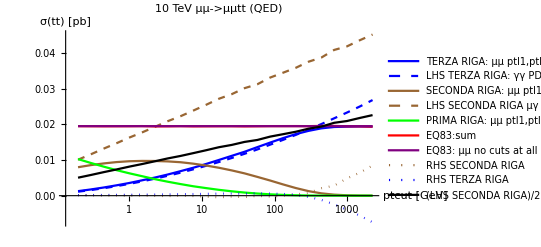

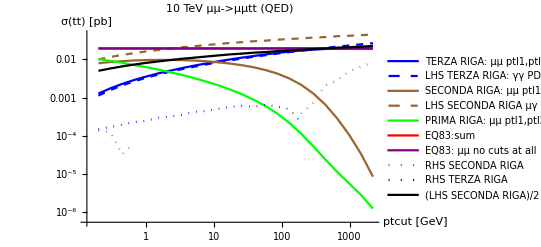

```mathematica
OPlinearplotEQ83=ListLogLinearPlot[{OPaa,aaWW,OPmua, OPnocutsmuaWW,OPmumu,OPsummed,OPtotal, OPRHS2nd83,OPRHS3rd,coeff[OPnocutsmuaWW,0.5]},Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt  (QED)",AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{"TERZA RIGA: μμ ptl1,ptl2 < ptcut","LHS TERZA RIGA: γγ PDF(scale=ptcut)", "SECONDA RIGA: μμ ptl1>ptcut ptl2<ptcut", "LHS SECONDA RIGA μγ (NOCUT) PDF(scale=ptcut)", "PRIMA RIGA: μμ ptl1,ptl2 > ptcut", "EQ83:sum"(*,"sum (PDF)"*),"EQ83: μμ no cuts at all","RHS SECONDA RIGA","RHS TERZA RIGA","(LHS SECONDA RIGA)/2"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,Purple,{Brown,Dotted},{Blue,Dotted},Black,{Red,Thickness->0.011},{Red,Dotted,Thickness->0.01}}]

OPlogplotEQ83=ListLogLogPlot[{OPaa,aaWW,OPmua, OPnocutsmuaWW,OPmumu,OPsummed,OPtotal, OPRHS2nd83,OPRHS3rd,coeff[OPnocutsmuaWW,0.5]},Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt (QED)",AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{"TERZA RIGA: μμ ptl1,ptl2 < ptcut","LHS TERZA RIGA: γγ PDF(scale=ptcut)", "SECONDA RIGA: μμ ptl1>ptcut ptl2<ptcut", "LHS SECONDA RIGA μγ (NOCUT) PDF(scale=ptcut)", "PRIMA RIGA: μμ ptl1,ptl2 > ptcut", "EQ83:sum"(*,"sum (PDF)"*),"EQ83: μμ no cuts at all","RHS SECONDA RIGA","RHS TERZA RIGA","(LHS SECONDA RIGA)/2"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,Purple,{Brown,Dotted},{Blue,Dotted},Black,{Red,Thickness->0.01},{Red,Dotted,Thickness->0.01}}]
```

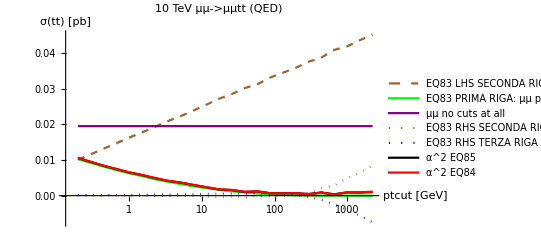

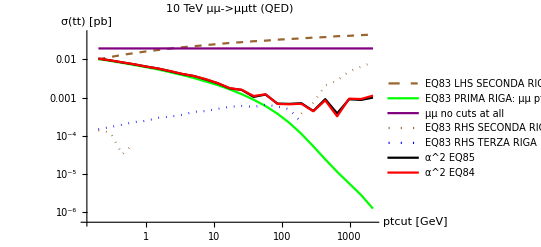

```mathematica
OPlinearplotEQ85=ListLogLinearPlot[{(*OPaa,aaWW,OPmua,*) OPnocutsmuaWW,OPmumu,(*OPsummed,*)OPtotal, OPRHS2nd83,OPRHS3rd(*,coeff[OPnocutsmuaWW,0.5]*),sum[sum[OPmumu,OPRHS2nd83],OPRHS3rd],diff[OPtotal,sum[OPddelta2S,aaWW]]},Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt (QED)",AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{(*"TERZA RIGA: μμ ptl1,ptl2 < ptcut","LHS TERZA RIGA: γγ PDF(scale=ptcut)", "SECONDA RIGA: μμ ptl1>ptcut ptl2<ptcut",*) "EQ83 LHS SECONDA RIGA μγ (NOCUT) PDF(scale=ptcut)", "EQ83 PRIMA RIGA: μμ ptl1,ptl2 > ptcut"(*, "EQ83:sum","sum (PDF)"*),"μμ no cuts at all","EQ83 RHS SECONDA RIGA","EQ83 RHS TERZA RIGA",(*"(LHS SECONDA RIGA)/2",*)"α^2 EQ85","α^2 EQ84"},PlotStyle->{(*Blue,{Blue,Dashed},Brown,*){Brown,Dashed},Green,(*Red,*)Purple,{Brown,Dotted},{Blue,Dotted},(*Black,*){Black,Thickness->0.01},{Red,Thickness->0.01}}]

OPlogplotEQ85=ListLogLogPlot[{(*OPaa,aaWW,OPmua,*) OPnocutsmuaWW,OPmumu,(*OPsummed,*)OPtotal, OPRHS2nd83,OPRHS3rd(*,coeff[OPnocutsmuaWW,0.5]*),sum[sum[OPmumu,OPRHS2nd83],OPRHS3rd],diff[OPtotal,sum[OPddelta2S,aaWW]]},Joined->True,InterpolationOrder->1,PlotLabel->"10 TeV μμ->μμtt (QED)",AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{(*"TERZA RIGA: μμ ptl1,ptl2 < ptcut","LHS TERZA RIGA: γγ PDF(scale=ptcut)", "SECONDA RIGA: μμ ptl1>ptcut ptl2<ptcut",*) "EQ83 LHS SECONDA RIGA μγ (NOCUT) PDF(scale=ptcut)", "EQ83 PRIMA RIGA: μμ ptl1,ptl2 > ptcut"(*, "EQ83:sum","sum (PDF)"*),"μμ no cuts at all","EQ83 RHS SECONDA RIGA","EQ83 RHS TERZA RIGA",(*"(LHS SECONDA RIGA)/2",*)"α^2 EQ85","α^2 EQ84"},PlotStyle->{(*Blue,{Blue,Dashed},Brown,*){Brown,Dashed},Green,(*Red,*)Purple,{Brown,Dotted},{Blue,Dotted},(*Black,*){Black,Thickness->0.01},{Red,Thickness->0.01}}]
```

```mathematica
Export["/Users/pagani/mu-vbf/massive_mu/plots_PDF/"<>nome<>"/EQ83/linearplot.pdf",linearplotEQ83]
Export["/Users/pagani/mu-vbf/massive_mu/plots_PDF/"<>nome<>"//EQ83/logplot.pdf",logplotEQ83]
Export["/Users/pagani/mu-vbf/massive_mu/plots_PDF/"<>nome<>"/EQ85/linearplot.pdf",linearplotEQ85]
Export["/Users/pagani/mu-vbf/massive_mu/plots_PDF/"<>nome<>"//EQ85/logplot.pdf",logplotEQ85]
```

/Users/pagani/mu-vbf/massive_mu/plots_PDF/PDF1sttryMSbar/EQ83/linearplot.pdf

/Users/pagani/mu-vbf/massive_mu/plots_PDF/PDF1sttryMSbar//EQ83/logplot.pdf

/Users/pagani/mu-vbf/massive_mu/plots_PDF/PDF1sttryMSbar/EQ85/linearplot.pdf

/Users/pagani/mu-vbf/massive_mu/plots_PDF/PDF1sttryMSbar//EQ85/logplot.pdf

```mathematica
Export["/Users/pagani/mu-vbf/massive_mu/plots_PDF/"<>nome<>"/EQ83/OPlinearplot.pdf",OPlinearplotEQ83]
Export["/Users/pagani/mu-vbf/massive_mu/plots_PDF/"<>nome<>"//EQ83/OPlogplot.pdf",OPlogplotEQ83]
Export["/Users/pagani/mu-vbf/massive_mu/plots_PDF/"<>nome<>"/EQ85/OPlinearplot.pdf",OPlinearplotEQ85]
Export["/Users/pagani/mu-vbf/massive_mu/plots_PDF/"<>nome<>"//EQ85/OPlogplot.pdf",OPlogplotEQ85]
```

/Users/pagani/mu-vbf/massive_mu/plots_PDF/PDF1sttryMSbar/EQ83/OPlinearplot.pdf

/Users/pagani/mu-vbf/massive_mu/plots_PDF/PDF1sttryMSbar//EQ83/OPlogplot.pdf

/Users/pagani/mu-vbf/massive_mu/plots_PDF/PDF1sttryMSbar/EQ85/OPlinearplot.pdf

/Users/pagani/mu-vbf/massive_mu/plots_PDF/PDF1sttryMSbar//EQ85/OPlogplot.pdf

```mathematica
conPDF83={aa,aaWW,mua, nocutsmuaWW,mumu,summed,total, RHS2nd83,RHS3rd,coeff[ nocutsmuaWW,0.5]};
```

```mathematica
conPDF85={(*aa,aaWW,mua,*) nocutsmuaWW,mumu,(*summed,*)total, RHS2nd83,RHS3rd(*,coeff[nocutsmuaWW,0.5]*),sum[sum[mumu,RHS2nd83],RHS3rd],diff[total,sum[ddelta2S,aaWW]],NPtotal};
```

```mathematica
OPconPDF83={OPaa,aaWW,OPmua, OPnocutsmuaWW,OPmumu,OPsummed,OPtotal, OPRHS2nd83,OPRHS3rd,coeff[OPnocutsmuaWW,0.5]};
```

```mathematica
OPconPDF85={(*OPaa,aaWW,OPmua,*) OPnocutsmuaWW,OPmumu,(*OPsummed,*)OPtotal, OPRHS2nd83,OPRHS3rd(*,coeff[OPnocutsmuaWW,0.5]*),sum[sum[OPmumu,OPRHS2nd83],OPRHS3rd],diff[OPtotal,sum[OPddelta2S,aaWW]]};
```